```mathematica
(*$Messages=$Output; *)
```

#### Packages

```mathematica
Needs["FourierSeries`"]
Needs["HypothesisTesting`"]
ParallelNeeds["FourierSeries`"]
ParallelNeeds["HypothesisTesting`"]
(*Note that this package has been forked to deal with boundary conditions*)
Get[FileNameJoin[{NotebookDirectory[],"mcmc.m"}]];
$Messages={};
```

#### Deterministic Model

```mathematica
(* Firing rate *)
Q[rate_,v_,β_,t_]:=rate/(1+Exp[-β*(v-t)])

(*Lateral Connectivity*)
W[x_,r1_,r2_,R1_]:=R1*r1 Exp[-1/2*x^2r1^2 ]-r2 Exp[-1/2*x^2r2^2];

(*Wave-Form*)
h[k_,s1_,s2_]:=s1 s2*Exp[-1/2*k^2*(s2)^2]

(*Non-Constant Part of FT{S}(k)*)
g[k_,c_,τ_,tp_,r1_,r2_, R2_]:=4 c^2  k^2 τ Abs[tp]/(1+c^2k^2tp^2)/(c^2τ^2k^2+(1-W[k,r1,r2, R2])^2)

(*Fourier transform of the synaptic kernel*)
ftS[k_,κ_, λ_,τ_,τprime_,tp_,ap_,fr_,β_,θ_,s1_,s2_,c_,r1_,r2_,R1_] :=Re[ κ/λ(1/(1-g[k,c,τ,tp,r1,r2,R1]*h[k,s1,s2]^2*ap^2*Exp[θ*β]*fr*β/(1+Exp[θ*β])^2*τprime/λ) -1)]
ftSrenorm[k_,κ_, λ_,τ_,τprime_,tp_,ap_,fr_,β_,θ_,s1_,s2_,c_,r1_,r2_,R1_] :=Re[ κ/λ(1/(1-g[k,c,τ,tp,r1,r2,R1]*h[k,s1,s2]^2*ap^2*Exp[θ*β]*fr*β/(1+Exp[θ*β])^2*τprime/λ) -1)]-κ/λ
S[x_,κ_, λ_,τ_,τprime_,tp_,ap_,fr_,β_,θ_,s1_,s2_,c_,r1_,r2_,R1_]:=Re[NInverseFourierTransform[ftS[k,κ, λ,τ,τprime,tp,ap,fr,β,θ,s1,s2,c,r1,r2,R1] ,k,x,Method->"GaussKronrodRule"]]
```

```mathematica
(*Set the default parameters*)
κ=0.001;
λ=0.001;
ap=1;
β=0.26;
θ=13;
s1=0.05;
fr=1;
τprime=100;
S2= ap*D[Q[fr,x,β,θ],x]/.x->0;
```

```mathematica
(*Width estimate*)
SWidth[τ_?NumericQ,tp_?NumericQ,s2_?NumericQ,c_?NumericQ,r1_?NumericQ,r2_?NumericQ,R1_?NumericQ]:=Abs[1/(10^-7+ArgMax[ftS[k,κ, λ,τ,τprime,tp,ap,fr,β,θ,s1,s2,c,r1,r2,R1],k])]
SWidth[τ_?NumericQ,tp_?#<=0&,s2_?NumericQ,c_?NumericQ,r1_?NumericQ,r2_?NumericQ,R1_?NumericQ]:=10^9

(*Stability function*)
stab[k_,τ_?NumericQ,tp_?NumericQ,s2_?NumericQ,c_?NumericQ,r1_?NumericQ,r2_?NumericQ,R1_?NumericQ]:=g[k,c,τ,tp,r1,r2,R1]*h[k,s1,s2]^2*ap^2*Exp[θ*β]*fr*β/(1+Exp[θ*β])^2*τprime/λ
stabMax[τ_?NumericQ,tp_?NumericQ,s2_?NumericQ,c_?NumericQ,r1_?NumericQ,r2_?NumericQ,R1_?NumericQ]:=Max[stab[Table[k,{k,0.0,10,0.01}],τ,tp,s2,c,r1,r2,R1]] 

(*Amplitude*)
SAmp[τ_?NumericQ,tp_?NumericQ,s2_?NumericQ,c_?NumericQ,r1_?NumericQ,r2_?NumericQ,R2_?NumericQ]:=NIntegrate[ftS[k,κ, λ,τ,τprime,tp,ap,fr,β,θ,s1,s2,c,r1,r2,R1]-κ/λ,{k,-Infinity,Infinity}]
```

### Estimation of Local Kernel using PfongPfang

The data is estimated from figure 1 and is the in the form {location (μm), Maximal PSP}

FittedModel[1.08248 ⅇ^(-30.082 x^2)-ⅇ^(-26.9677 x^2)]

| Estimate | Standard Error | Confidence Interval
R1est | 1.08248 | 0.010192 | {1.05418,1.11078}
r1est | 0.128923 | 0.012295 | {0.094787,0.16306}
r2est | 0.136164 | 0.0136187 | {0.0983525,0.173976}

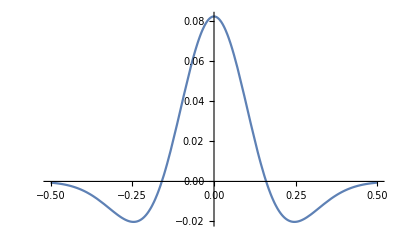

```mathematica
Fig1LM={{-450, -17.5}, {-300, -10},{-150, -20}, {0, 80}, {150, -5}, {300, -25}, {450, 0}};
Fig1RC ={{-450,-1}, {-300,1},{-150,40}, {0, 85}, {150, 5}, {300, -30}, {450, 10}};
dataAv = (Fig1LM + Fig1RC)/2;
data=Table[{dataAv[[i]][[1]]/1000,dataAv[[i]][[2]]/1000},{i,1,Length[dataAv]}];
model[x_,R1_,r1_,r2_]:=R1*Exp[-x^2/(2r1^2)]-Exp[-x^2/(2 r2^2)]
fit=NonlinearModelFit[data, model[x, R1est,r1est,r2est], {R1est,r1est,r2est},x]
fit["ParameterConfidenceIntervalTable"]
Plot[fit[x],{x,-0.5,0.5}]
```

## Image Generation

### Model Summary

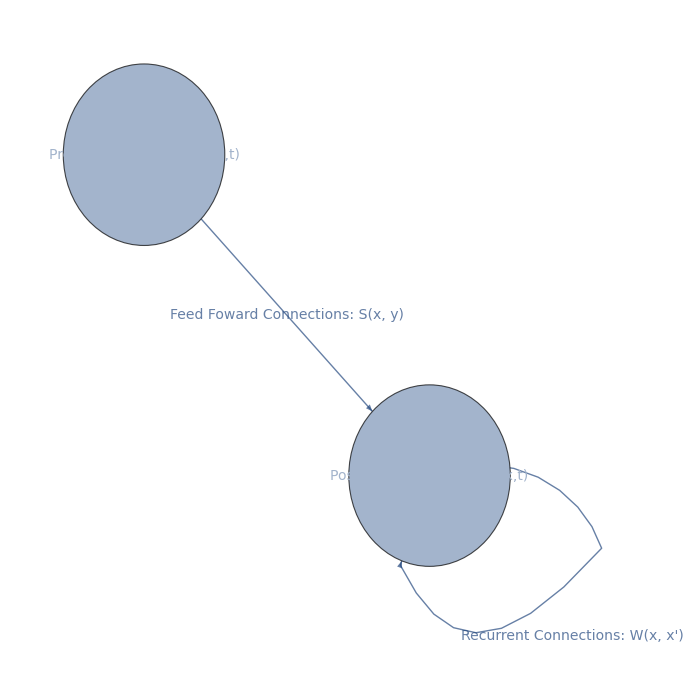

```mathematica
GraphPlot[{{1->1,Style["Recurrent Connections: W(x, x')",14]},{2->1,Style["Feed Foward Connections: S(x, y)", 14]}}
,VertexLabels->{1-> Placed[{Style["Post-Synaptic Activity: u(x,t)", 14, Italic]},Center], 2->Placed[{Style["Pre-Synaptic Activity: a(y,t)", 14, Italic]},Center]}, 

VertexSize->0.4,

VertexShapeFunction->"Circle" ,
VertexCoordinates->{1->{0.5,0.0},2->{0,0.5}},
EdgeWeight->{1,20},
GraphLayout->{"SpringElectricalEmbedding"},
ImageSize->{700,700}]
```

### Retinotopy

```mathematica
LateralConnectionsCurvilinear[x_,y_]:=2*Exp[- Abs[(x-y^3)]]-1*Exp[-Abs[ (x-y^3)/2]]
LateralConnectionsLinear[x_,y_]:=2*Exp[- Abs[(x-y)]]-1*Exp[-Abs[ (x-y)/2]]

Rasterize[ContourPlot[LateralConnectionsCurvilinear[x,y],{x,-1,1},{y,-1,1},ColorFunction->"TemperatureMap",
PlotLabel→Style["Wizards Hat Lateral Connection Pattern: p(y)=y^3, ρ=0", "Section", 14],
FrameLabel→{Style["x", Bold, 12],Style["y", Bold, 12]},PlotLegends→BarLegend[Automatic,LegendMarkerSize→180,LegendMargins→2,LegendLabel→"Synaptic \n Weight"]], RasterSize→800, ImageSize→400]

Rasterize[ContourPlot[LateralConnectionsLinear[x,y],{x,-1,1},{y,-1,1},ColorFunction->"TemperatureMap",
PlotLabel→Style["Wizards Hat Lateral Connection Pattern: p(y)=y, ρ=0", "Section", 14],
FrameLabel→{Style["x", Bold, 12],Style["y", Bold, 12]},
PlotLegends→BarLegend[Automatic,LegendMarkerSize→180,LegendMargins→2,LegendLabel→"Synaptic \n Weight"]], RasterSize→800, ImageSize→400]
```

-Graphics-

-Graphics-

### Typical Organisations

```mathematica
τ = 0.055;
tp = 0.6;
s2 = 0.5;
c = 0.3;
r1 = 0.129;
r2 = 0.136;
R1 = 1.078;
```

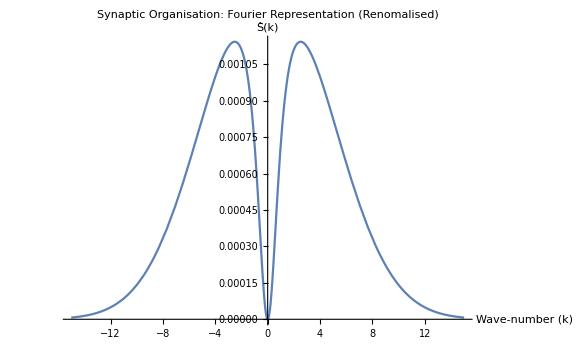

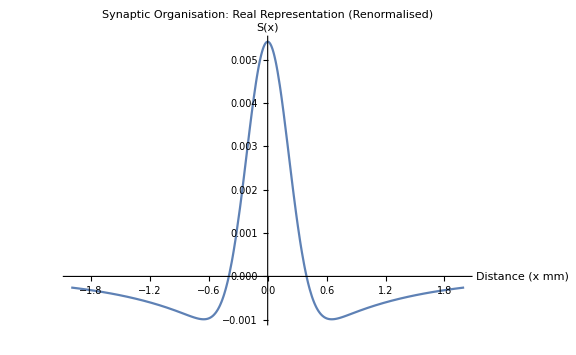

```mathematica
Plot[ftS[k,κ, λ,τ,τprime,tp,ap,fr,β,θ,s1,s2,c,r1,r2,R1], {k, -15,15}, PlotRange->All, PlotLabel->Style["Synaptic Organisation: Fourier Representation (Renomalised)", "Section", 18], AxesLabel->{Style["Wave-number (k)", 14, Black], Style["Ŝ(k)", 14, Black]} ,ImageSize->Large]
Quiet[Plot[S[x,κ, λ,τ,τprime,tp,ap,fr,β,θ,s1,s2,c,r1,r2,R1], {x, -2,2}, PlotRange->All,PlotLabel->Style["Synaptic Organisation: Real Representation (Renormalised)", "Section", 18], AxesLabel->{Style["Distance (x mm)", 14, Black],Style[ "S(x)", 14, Black]} ,ImageSize->Large]]
```

### Stability Surface, Width, and Amplitudes

```mathematica
(*specify plot parameters*)
min=0.0;
max=10.0;
imsize={600,500};
barpos={1.05,0.5};
stabpos={1.05,0.20};
rastersize=1000;
finalimsize=500;
regionfunction=Evaluate[Max[stab[Table[k,{k,0,10,0.01}],c,r,s]]/.{c->#1,r->#2,s->#3}]&;
regionfunction=Evaluate[Max[stab[Table[k,{k,0,10,0.01}],c,r,s]]/.{c->#1,r->#2,s->#3}]&;
regioncap=1.01;
imtext=15;
titletext=25;
```

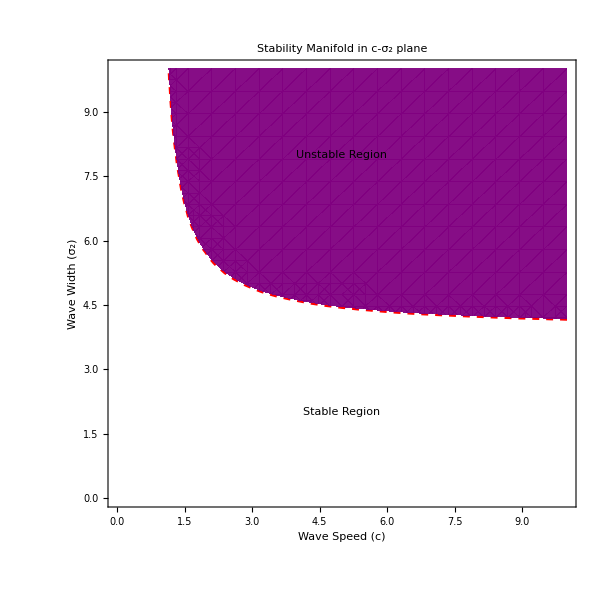

```mathematica
(*Stability surface*)
Show[ContourPlot[stabMax[τ,tp,s2,c,r1,r2,R1]==1, {c,min,max},{s2,min,max},
AxesOrigin->{min,min},
FrameLabel->{Style["Wave Speed (c)", Bold, imtext],Style["Wave Width (σ_2)", Bold, imtext]},
PlotLabel->Style["Stability Manifold in c-σ_2 plane", "Section", titletext],
Mesh->None,
ContourStyle->Directive[Red,Dashed,Bold],
ImageSize->imsize
],
RegionPlot[stabMax[τ,tp,s2,c,r1,r2,R1]>regioncap,{c,min,max},{s2,min,max},
BoundaryStyle->None,PlotStyle->Directive[Opacity[0.95],Purple],
ImageSize->imsize],
Epilog->{Inset[Framed[Style["Unstable Region",20],Background->White],{5,8}],Inset[Framed[Style["Stable Region",20],Background->White],{5,2}]}]
```

```mathematica
ContourPlot[SWidth[τ,tp,s2,c,r1,r2,R1] ,{c,0.001,1.0},{s2,0.001,1.0},
PlotLabel->Style[StringForm["Synaptic Organisation Width: c-σ_2 plane"], "Section", titletext],
FrameLabel->{Style["Wave Speed (c)", Bold, imtext],Style["Wave Width (σ_2)", Bold, imtext]},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->180,LegendMargins->2,LegendLabel->Style["Ω",imtext]],barpos],
ImageSize->imsize]

ContourPlot[SWidth[τ,tp,s2,c,r1,r2,R1] ,{τ,0.001,1.0},{tp,0.0,100.0},
PlotLabel->Style[StringForm["Synaptic Organisation Width: τ-t_p plane"], "Section", titletext],
FrameLabel->{Style["Activity Time Scale (τ)", Bold, imtext],Style["Plasticity Window (t_p)", Bold, imtext]},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->180,LegendMargins->2,LegendLabel->Style["Ω",imtext]],barpos],
ImageSize->imsize]

ContourPlot[SWidth[τ,tp,s2,c,r1,r2,R1] ,{r1,0.001,0.5},{r2,0.001,0.5},
PlotLabel->Style[StringForm["Synaptic Organisation Width: r_1-r_2 plane"], "Section", titletext],
FrameLabel->{Style["Recurrent Excitation Length (r_1)", Bold, imtext],Style["Recurrent Inhibition Length (r_2)", Bold, imtext]},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->180,LegendMargins->2,LegendLabel->Style["Ω",imtext]],barpos],
ImageSize->imsize]

ContourPlot[SWidth[τ,tp,s2,c,r1,r2,R1] ,{R1,0.001,1.0},{r1,0.001,1.0},
PlotLabel->Style[StringForm["Synaptic Organisation Width: R_1-r_1 plane"], "Section", titletext],
FrameLabel->{Style["Recurrent Amplitude (R_1)", Bold, imtext],Style["Reccurent Excitation Scale (r_1)", Bold, imtext]},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->180,LegendMargins->2,LegendLabel->Style["Ω",imtext]],barpos],
ImageSize->imsize]
```

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

## Regression Fits

We would like to fit our model to a sample of wild-type mice and β2 mice. A reliable measurement of wave properties comes from Stafford et al (2009), and a reliable arbor size from Dhande et al (2011). Since these are two different data sets it is most appropriate to choose a measurement error model with categories of β2 and Wild-Type. In this section we are going to use an MCMC fitted model to regress on the data. We are choosing seconds as the time scale, and mm as the length scale.

#### Data

```mathematica
arboreasurements={{2.4*10^5,0.24*10^5},{8.9*10^5,0.93*10^5}};
wavespeedeasurements={{130.0, 15.0},{170.0, 30.0}};
wavelengthmeasurements={{225.0, 25.0},{400.0,25.0}};
```

We now do the necessary unit conversions to be appropriate for the model. We assume that the wave speed is measured in mm and therefore the area measurements should be scaled by a factor of ten so that s2 is also on the scale of millimeters.

```mathematica
areamicronstolengthmm[area_]:=Sqrt[(area)/Pi*10^-12]*10^3
lengthmicronstolengthmm[length_]:=length*10^-3
Npoints=Length[arboreasurements];
arborestimates=Table[{NormalDistribution,0.5*areamicronstolengthmm[arboreasurements[[i,1]]],0.5*areamicronstolengthmm[arboreasurements[[i,2]]] }, {i, 1, Npoints}];
s2estimates=Table[{NormalDistribution,0.5*lengthmicronstolengthmm[wavelengthmeasurements[[i,1]]],0.5*lengthmicronstolengthmm[wavelengthmeasurements[[i,2]]] }, {i, 1, Npoints}];
wavespeedestimates=Table[{NormalDistribution,lengthmicronstolengthmm[wavespeedeasurements[[i,1]]],lengthmicronstolengthmm[wavespeedeasurements[[i,2]]] }, {i, 1, Npoints}];
```

We can now define the likelihood function given a data point is from a particular category and under the assumption that the other parameters are independent of these particular mutations. Most of the parameters do not affect the size and can therefore be excluded, some of the parameters can be estimated (r1, r2) while others we attach an uninformative prior (τ, tp, R1). We start by defining the deterministic model, priors, and categorical likelihood. First make a convenience wrapper for all of the data.

```mathematica
estimates={arborestimates,s2estimates ,wavespeedestimates};
symfunction[j_,w_,s_,c_]:=If[j==1,w,If[j==2,s,If[j==3,c]]];
pdfdata[i_,estimates_,w_,s_,c_]:=Product[PDF[estimates[[j,i]][[1]][estimates[[j,i]][[2]], estimates[[j,i]][[3]]]][symfunction[j,w,s,c]],{j,1,Length[estimates]}]
```

```mathematica
estimates[[All,All,2]]//MatrixForm;
estimates[[All,All,3]]//MatrixForm;
pdfdata[1,estimates,w,s,c];
```

#### Priors

Need to restrict these to the positive domain which is a problem for the MCMC package. Create a new PDF and use the HeavisideTheta function to get a functional evaluatable form for the MCMC package and then add a small perturbation to avoid a simplification by the WolframKernel.

```mathematica
pτ=Function[x, 1/(1-0.0001)(HeavisideTheta[x-0.0001]-HeavisideTheta[x-1])];(*PDF[NormalDistribution[0.1,0.01]];*)
ptp=Function[x, 1/(5-0.0001) (HeavisideTheta[x-0.0001]-HeavisideTheta[x-5])];(*PDF[NormalDistribution[0.1,1]];*)

(*Informative Priors*)
pR1=PDF[NormalDistribution[1.08,0.01]];
(*Function[x, 1/10(HeavisideTheta[x]-HeavisideTheta[x-10])];*)(*PDF[NormalDistribution[0.5,0.1]];(*NormalDistribution[0.67,0.05];*)(*estimated from PfongPfang*)*)
pr1=PDF[NormalDistribution[0.13,0.012]]; 
pr2 =PDF[NormalDistribution[0.14,0.014]];

Clear[pdf];
pdf[fun_]:=Simplify[Evaluate[fun[#]], #>0]*HeavisideTheta[#]&;
priorpdfs={pτ,ptp,pr1,pr2,pR1};
```

#### Likelihood Model

There are quite a few parameters so we shall assemble the likelihood in the following form: independent variables sampled from measurement distributions, likelihood of dependent variable under normal error assumption, and priors for parameters.

```mathematica
L[τ_,tp_,s2_,c_,r1_,r2_,R1_,estimates_,i_]:=pdfdata[i,estimates,SWidth[τ,tp,s2,c,r1,r2,R1],s2,c]*
pdf[pτ][τ]*pdf[pr1][r1]*pdf[pr2][r2]*pdf[pR1][R1]*pdf[ptp][tp]
```

Now we define the log-likelihood for all of the data. This is what we will be minimising via MCMC.

```mathematica
$Messages={};
Clear[logL,loglikelihood,τ,tp,s2,c,r1,r2,R1]
logL[τ_,tp_,s2_,c_,r1_,r2_,R1_]:=Evaluate[Simplify[PowerExpand[Sum[Log[L[τ,tp,s2,c,r1,r2,R1,estimates,i]],{i,1,Npoints}]]]];
loglikelihood=Evaluate[logL[τ,tp,s2,c,r1,r2,R1]]
```

-12078.9+766.667 c-2777.78 c^2+1805.56 r1-6944.44 r1^2+21600. R1-10000. R1^2+1428.57 r2-5102.04 r2^2+2000. s2-6400. s2^2+2 Log[HeavisideTheta[r1]]+2 Log[HeavisideTheta[R1]]+2 Log[HeavisideTheta[r2]]+2 Log[-HeavisideTheta[-5+tp]+HeavisideTheta[-0.0001+tp]]+2 Log[HeavisideTheta[tp]]+2 Log[-HeavisideTheta[-1+τ]+HeavisideTheta[-0.0001+τ]]+2 Log[HeavisideTheta[τ]]+108.32 SWidth[τ,tp,s2,c,r1,r2,R1]-329.361 SWidth[τ,tp,s2,c,r1,r2,R1]^2

#### MCMC

Now we perform the MCMC giving it lots of room to breath. We need to check that the MCMC did converge which probably will entail running several chains and doing some convergence measures. We will do 8 chains corresponding to two initializations in each of the sample basins and run for 100000 trials. Once each of the chains are complete we compute the Rubin-Gelman statistic to see if the MCMC has converged and combine all of the parameter runs together. Then we can plot the distributions, time-series, histogram and pick most likely parameters on all parameters that haven’t been estimated from data - it would be nonsensical to have a single “best” parameter when we know that there are four basins (categories) corresponding to the experimental classes. Whether any of these other parameters in the model correlate with these experimental categories remains to be seen, but as a reasonable judgement we are assuming that they are pretty independent: β2  knock-out is probably not going to change the time scale on which plasticity occurs, for example.

```mathematica
Clear[res, pw]
SeedRandom[9876543210];
jumps=Re[0.25*Table[If[i≤Length[estimates]-1, estimates[[i+1]][[2]][[3]], Chop[Sqrt[Integrate[x^2 priorpdfs[[i-Length[estimates]+1]][x], {x,-∞,∞}] -Integrate[x priorpdfs[[i-Length[estimates]+1]][x] ,{x,-∞,∞}]^2]]],{i,1,7}]];
nchains=6;
domain =Reals;
ip=Table[(1+0.01*(RandomReal[]))*If[i≤Length[estimates]-1, estimates[[i+1]][[Mod[j-1,Npoints]+1]][[2]], ArgMax[priorpdfs[[i-Length[estimates]+1]][x],x]],{i,1,7},{j,1,nchains}];
ip=Table[(1+0.1*(RandomReal[]))*If[i≤Length[estimates]-1, estimates[[i+1]][[Mod[j-1,Npoints]+1]][[2]], Chop[Integrate[x priorpdfs[[i-Length[estimates]+1]][x] ,{x,-∞,∞}]]],{i,1,7},{j,1,nchains}];

ntrials=Round[10^5];
(*Generate a new test, or load an old one*)
generate=True;
(*Create a parallel worker*)
pw[j_,ntrials_,domain_, jumps_,ip_]:=Block[{τ,tp,s2,c,r1,r2,R1},$Messages={};
MCMC[loglikelihood,{{s2,ip[[1,j]],jumps[[1]],domain},
{c,ip[[2,j]],jumps[[2]],domain},
{τ,ip[[3,j]],jumps[[3]],domain},
{tp,ip[[4,j]],jumps[[4]],domain},
{r1,ip[[5,j]],jumps[[5]],domain},
{r2,ip[[6,j]],jumps[[6]],domain},
{R1,ip[[7,j]],jumps[[7]],domain}
},ntrials]]

DistributeDefinitions[pw];ParallelEvaluate[pw=pw;];
DistributeDefinitions[MCMC];ParallelEvaluate[MCMC=MCMC;];
Clear[mcmcrun,res];
ip//MatrixForm
```

(0.117236 | 0.207387 | 0.116959 | 0.208931 | 0.113813 | 0.209597
0.133057 | 0.171515 | 0.13013 | 0.183917 | 0.139854 | 0.172747
0.538064 | 0.504462 | 0.507623 | 0.537135 | 0.512652 | 0.522412
2.62213 | 2.57923 | 2.64591 | 2.69364 | 2.62704 | 2.52071
0.141677 | 0.134354 | 0.142166 | 0.136676 | 0.130213 | 0.14089
0.145242 | 0.148862 | 0.1539 | 0.146037 | 0.146203 | 0.144249
1.1879 | 1.08632 | 1.14697 | 1.1466 | 1.11972 | 1.11163)

```mathematica
AbsoluteTiming[If[generate,res=ParallelTable[pw[j,ntrials,domain,jumps,ip], {j,1,Dimensions[ip][[2]]}];
Table[mcmcrun[i]=res[[i]], {i,1,Dimensions[ip][[2]]}];
DeleteFile[NotebookDirectory[]<>"chains"<>".m"];
Save[NotebookDirectory[]<>"chains"<>".m",mcmcrun]];]
```

{1074.57,Null}

```mathematica
(*collect results*)
Get[NotebookDirectory[]<>"chains"<>".m"];
mcmcrun[1]["ParameterRunPlots"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Generate the Gelman-Rubin convergence diagnostic

```mathematica
(*generate the entire posterior over all chains for each parameter*)
posterior=Table[Flatten[Join[Table[mcmcrun[i]["ParameterRun"][[1;;ntrials,j ]], {i,1,nchains}]]],{j,1,Length[mcmcrun[1]["Parameters"]]}];
(*generate chain means and variances *)
chainmeans= Table[Mean[mcmcrun[i]["ParameterRun"][[1;;ntrials,j ]]], {i,1,nchains},{j,1,Length[mcmcrun[1]["Parameters"]]}];
chainvariance= Table[Variance[mcmcrun[i]["ParameterRun"][[1;;ntrials,j ]]], {i,1,nchains},{j,1,Length[mcmcrun[1]["Parameters"]]}];

(*calculate the Between Chain and Within Chain variances for each parameter*)
Bvar=Table[ntrials/(nchains-1)*Sum[(chainmeans[[i,j]]-Mean[chainmeans[[All,j]]])^2,{i,1,nchains}],{j,1,Length[mcmcrun[1]["Parameters"]]}];
Wvar=Table[Mean[chainvariance[[All,j]]],{j,1,Length[mcmcrun[1]["Parameters"]]}];

(*Caculate the pooled variance and the PRSF*)
Vbar=(ntrials-1)/ntrials * Wvar +( nchains+1)/(ntrials*nchains)*Bvar;
PRSF=Sqrt[Vbar/Wvar]
```

{1.0026,1.00291,1.00299,1.00095,1.00063,1.00063,1.00174}

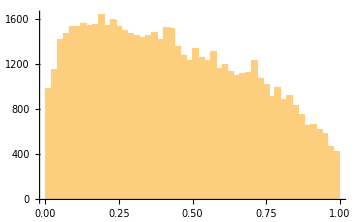
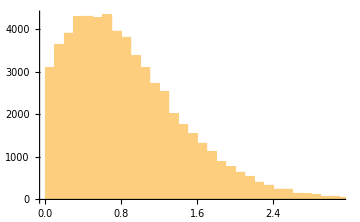
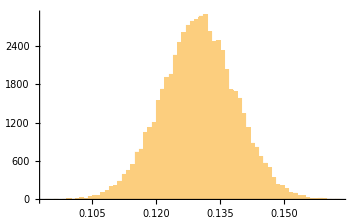
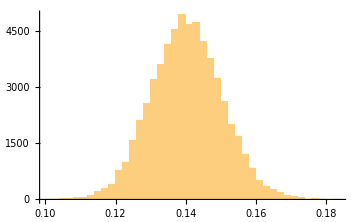
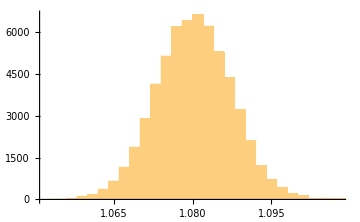

```mathematica
nbins=50;
Table[Histogram[posterior[[i]], nbins, ImageSize->Medium], {i,3,Length[posterior]}]
```

#### Posteriors

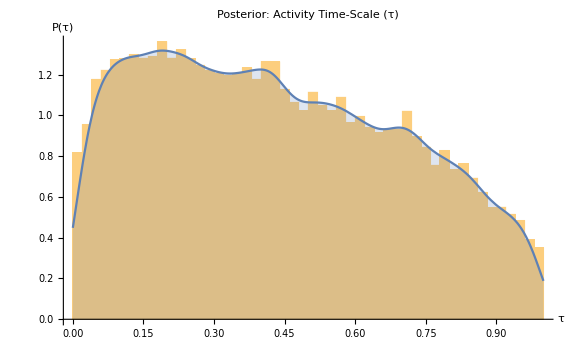

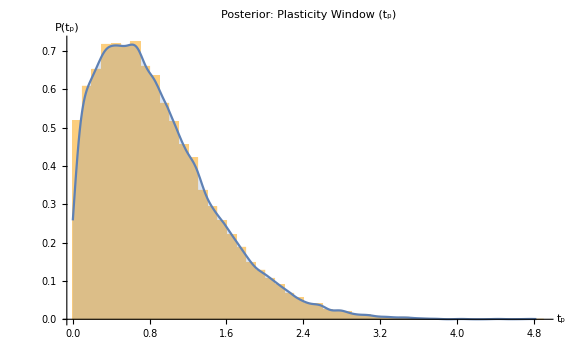

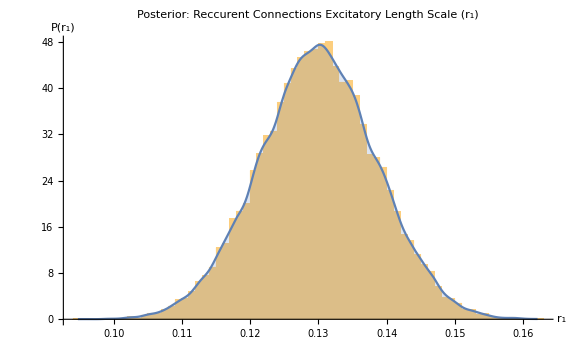

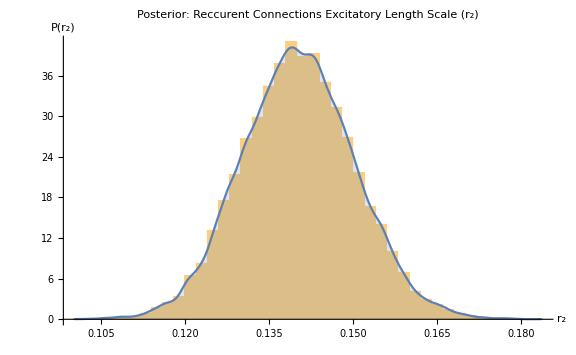

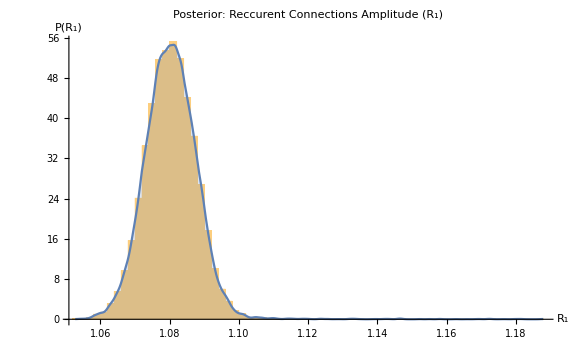

```mathematica
imtext=9;
sectext=14;
Show[Histogram[posterior[[3]], 50, "ProbabilityDensity"], Plot[PDF[SmoothKernelDistribution[posterior[[3]]]][x],{x,Min[posterior[[3]]],Max[posterior[[3]]]}, Filling->Axis,PlotRange->{0,All}],ImageSize->Large,PlotRange->All, PlotLabel->Style[StringForm["Posterior: Activity Time-Scale (τ)"], "Section", sectext],
AxesLabel->{Style["τ", Bold, imtext],Style["P(τ)", Bold, imtext]}]
Show[Histogram[posterior[[4]], 50, "ProbabilityDensity"], Plot[PDF[SmoothKernelDistribution[posterior[[4]]]][x],{x,Min[posterior[[4]]],Max[posterior[[4]]]}, Filling->Axis,PlotRange->{0,All}],ImageSize->Large,PlotRange->All, PlotLabel->Style[StringForm["Posterior: Plasticity Window (t_p)"], "Section", sectext],
AxesLabel->{Style["t_p", Bold, imtext],Style["P(t_p)", Bold, imtext]}]
Show[Histogram[posterior[[5]], 50, "ProbabilityDensity"], Plot[PDF[SmoothKernelDistribution[posterior[[5]]]][x],{x,Min[posterior[[5]]],Max[posterior[[5]]]}, Filling->Axis,PlotRange->{0,All}],ImageSize->Large,PlotRange->All, PlotLabel->Style[StringForm["Posterior: Reccurent Connections Excitatory Length Scale (r_1)"], "Section", sectext],
AxesLabel->{Style["r_1", Bold, imtext],Style["P(r_1)", Bold, imtext]}]
Show[Histogram[posterior[[6]], 50, "ProbabilityDensity"], Plot[PDF[SmoothKernelDistribution[posterior[[6]]]][x],{x,Min[posterior[[6]]],Max[posterior[[6]]]}, Filling->Axis,PlotRange->{0,All}],ImageSize->Large,PlotRange->All, PlotLabel->Style[StringForm["Posterior: Reccurent Connections Excitatory Length Scale (r_2)"], "Section", sectext],
AxesLabel->{Style["r_2", Bold, imtext],Style["P(r_2)", Bold, imtext]}]
Show[Histogram[posterior[[7]], 50, "ProbabilityDensity"], Plot[PDF[SmoothKernelDistribution[posterior[[7]]]][x],{x,Min[posterior[[7]]],Max[posterior[[7]]]}, Filling->Axis,PlotRange->{0,All}],ImageSize->Large,PlotRange->All, PlotLabel->Style[StringForm["Posterior: Reccurent Connections Amplitude (R_1)"], "Section", sectext],
AxesLabel->{Style["R_1", Bold, imtext],Style["P(R_1)", Bold, imtext]}]
```

#### Goodness of Fit

We need to establish a goodness of fit for our model. We can calculate the R2 coefficient but in general this is not a good measure of a non-linear model. The p-value is then the rejection of the null hypothesis which is that the mean is the best predictor. The R2 coefficients are calculated as the ratio of the data error to the residual error. The p-value takes the assumption that the data are distributed around the data mean with standard deviation of the data error, to reject the null-hypothesis we show the residual errors form a significantly different distribution than simply the mean which is a t-test. For n data points the t-statistic can be calculated as a function of the R2:

```mathematica
(*find the best fit*)
findmaxlikelihoodhistogram[data_,b_]:=Block[{counts,bins,binIdx,max}, {bins,counts}=HistogramList[data,b];binIdx=Position[counts,Max[counts]][[1]][[1]];max=bins[[binIdx]];max*1.0];
findmaxlikelihood[posterior_]:=Block[{dist,x}, dist=PDF[SmoothKernelDistribution[posterior]];x/. FindMaximum[dist[x],{x,findmaxlikelihoodhistogram[posterior,nbins]}][[2]]];
bestfit=Table[findmaxlikelihood[posterior[[j]]],{j,1,Dimensions[ip][[1]]}];
params=bestfit[[3;;Length[bestfit]]]
model[s2_,c_]:=Evaluate[SWidth[#1, #2,s2,c,#3,#4,#5]&@@params];
```

{0.18971,0.613546,0.130144,0.139141,1.08116}

```mathematica
findmaxlikelihoodhistogram[posterior[[4]],nbins]
```

0.4

```mathematica
Print["Data"]
modelpredictors=1.0*Table[model[estimates[[2]][[i]][[2]],estimates[[3]][[i]][[2]]],{i,1,Npoints}]
widthdata=Table[estimates[[1]][[i]][[2]],{i,1,Npoints}]
widthvar=Table[estimates[[1]][[i]][[3]],{i,1,Npoints}]^2;
weights=Table[1/estimates[[1]][[i]][[3]]^2,{i,1,Npoints}];
Print["Variance"]
modelvariance=Total[(modelpredictors-widthdata)^2]/Length[widthdata]
datavariance=Total[(widthdata-Mean[widthdata])^2]/Length[widthdata]
weighteddatavariance=Total[(widthdata-Total[widthdata*weights]/Total[weights])^2]/Length[widthdata];
Print["Fit"]
R2=1-modelvariance/weighteddatavariance
R2=1-modelvariance/datavariance;
```

Data

{0.133649,0.223048}

{0.138198,0.266128}

Variance

0.000938292

0.00409152

Fit

0.829851